### dopplerB_forward.nb Forward model Doppler equation Carl Tape and Bella Seppi October 20, 2025

### Example values for a Doppler curve

```mathematica
SetParms:=(c=343.;v=50;t0=215.;d0=1000.;fs=110.;tp0=t0+d0/c;)
ClearParms:=Clear[c,v,t0,d0,fs,tp0,tp]
```

```mathematica
ClearParms
```

### clear functions (optional)

```mathematica
Clear[t,Ft,SinGamma,FfactorA,Ffactor,t0]
```

### potentially these could be help with simplifications, but we did not use them explicitly

```mathematica
DopplerAssumptions={d0>=0,c>0,v>=0,fs>0,t0∈Reals};
```

## Main equations

### from dopplerA_solve.nb tp is the dependent variable and should be thought of as time in the spectrogram.

```mathematica
t[v_,t0_,d0_,c_,tp_]:=((tp-t0)-d0/c √((1-v^2/c^2)+((v(tp-t0))/d0)^2))/(1-v^2/c^2)
```

### forward model F(m, tp), split into subequations (m = (v, t0, d0, c)) FfactorA < 0, Ffactor < 1, and Ft > fs.

```mathematica
SinGamma[v_,t0_,d0_,c_,tp_]:=(-v t[v,t0,d0,c,tp])/(√(d0^2+(v t[v,t0,d0,c,tp])^2))
FfactorA[v_,t0_,d0_,c_,tp_]:=v/c SinGamma[v,t0,d0,c,tp]
Ffactor[v_,t0_,d0_,c_,tp_]:=1-FfactorA[v,t0,d0,c,tp];
Ft[v_,t0_,d0_,fs_,c_,tp_]:=fs/Ffactor[v,t0,d0,c,tp];
```

### Function in terms of t:

```mathematica
SinGammat[v_,d0_,t_]:=(-v t)/(√(d0^2+(v t)^2))
```

### Common factor:

```mathematica
vcfac[v_,c_]:=1-(v/c)^2
```

## Derivatives with respect to sensor time tp

### If you want explicit expressions, you can use this function to reduce the text:

```mathematica
(*G[v_,t0_,d0_,c_,tp_]:=√((-d0^2 v^2+c^2 (d0^2+(tp-t0)^2 v^2))/c^4)*)
```

```mathematica
(*G[v_,t0_,d0_,c_,tp_]:=√(1-v^2/c^2+((t0-tp)^2 v^2)/d0^2)*)
```

### Derivative expressions

```mathematica
(* FullSimplify[D[Ft[v,t0,d0,fs,c,tp],{tp,1}]]*)
```

```mathematica
(*FullSimplify[D[Ft[v,t0,d0,fs,c,tp],{tp,2}]]*)  (* this calculation did not finish in >12 hours *)
```

```mathematica
(* Simplify[D[Ft[v,t0,d0,fs,c,tp],{tp,2}]] *)
```

```mathematica
(* Simplify[D[Ft[v,t0,d0,fs,c,tp],{tp,3}]] *)
```

```mathematica
D1F[v_,t0_,d0_,fs_,c_,tp_]:=D[Ft[v,t0,d0,fs,c,t],t]/. t->tp
D2F[v_,t0_,d0_,fs_,c_,tp_]:=D[Ft[v,t0,d0,fs,c,t],{t,2}]/. t->tp
D3F[v_,t0_,d0_,fs_,c_,tp_]:=D[Ft[v,t0,d0,fs,c,t],{t,3}]/. t->tp
```

## Exploration of forward model equations

```mathematica
Ft[v,t0,d0,fs,c,t0+d0/c]
```

fs

### The special case of tp = tp0 gives t(tp0) = 0

```mathematica
FullSimplify[t[v,t0,d0,c,t0+d0/c]]
```

0

### The special case of tp = t0 gives t(t0) < 0

```mathematica
FullSimplify[t[v,t0,d0,c,t0]]
```

-d0/(c √(1-v^2/c^2))

```mathematica
t0fun[v_,d0_,c_]:=-d0/c(vcfac[v,c])^(-1/2)
```

```mathematica
FullSimplify[FfactorA[v,t0,d0,c,t0]]
```

(d0 v^2)/(c^2 √((c^2 d0^2)/(c^2-v^2)) √(1-v^2/c^2))

```mathematica
(d0 v^2)/(c^2 d0 √(c^2/(c^2-v^2)) √(1-v^2/c^2));
```

```mathematica
v^2/(c^2 √(1/(1-v^2/c^2)) √(1-v^2/c^2));
```

```mathematica
FfactorAt0[v_,c_]:=(v/c)^2
```

### Find the limiting values for Fapproach (higher frequency; flying toward) Frecede (lower frequency; flying away). (This takes a minute.)

```mathematica
(*Limit[Ft[v,t0,d0,fs,c,tp],tp->-Infinity]
Limit[Ft[v,t0,d0,fs,c,tp],tp->Infinity]*)
```

### These can be simplified greatly (with assumptions on c and v).

```mathematica
Fapproach[v_,fs_,c_]:=fs/(1-v/c)
```

```mathematica
Frecede[v_,fs_,c_]:=fs/(1+v/c)
```

```mathematica
(*Fmean[v_,fs_,c_]:=(Fapproach[v,fs,c]+Frecede[v,fs,c])/2*)
```

```mathematica
Fmean[v_,fs_,c_]:=fs 1/vcfac[v,c]
```

```mathematica
(*Frange[v_,fs_,c_]:=Fapproach[v,fs,c]-Frecede[v,fs,c]*)
```

```mathematica
Frange[v_,fs_,c_]:=((2 fs v)/c) 1/vcfac[v,c]
```

```mathematica
Simplify[Frange[v,fs,c]]
Simplify[Fapproach[v,fs,c]-Frecede[v,fs,c]]
```

(2 c fs v)/(c^2-v^2)

(2 c fs v)/(c^2-v^2)

### Key: the central frequency occurs at t’ = t0:

```mathematica
Fmean[v,fs,c]
FullSimplify[Ft[v,t0,d0,fs,c,t0]]
```

fs/(1-v^2/c^2)

(c^2 d0 fs)/(c^2 d0-v^2 √((c^2 d0^2)/(c^2-v^2)) √(1-v^2/c^2))

```mathematica
(c^2 d0 fs)/(c^2 d0-v^2 d0 √(c^2/(c^2-v^2)) √(1-v^2/c^2));
```

```mathematica
(c^2 d0 fs)/(c^2 d0-v^2 d0 √(1/(1-v^2/c^2)) √(1-v^2/c^2));
```

```mathematica
(c^2 fs)/(c^2-v^2);
```

```mathematica
fs/(1-v^2/c^2);
```

### OPTIONAL Let ε = v/c. Re-write as a series in ε, then consider approximations.

```mathematica
expr=Frange[v,fs,c];
exprSub=expr/. v->ε c;
FullSimplify[exprSub]
Series[exprSub,{ε,0,4}]//Normal//FullSimplify
Series[exprSub,{ε,0,2}]//Normal//FullSimplify
```

-(2 fs ε)/(-1+ε^2)

2 fs ε (1+ε^2)

2 fs ε

```mathematica
Frangeapprox2[v_,fs_,c_]:=2 fs (v/c)
```

```mathematica
Frangeapprox4[v_,fs_,c_]:=Frangeapprox2[v,fs,c](1+(v/c)^2)
```

### Here’s full simplification of Ft[ ], though I don’t think it helps:

```mathematica
(*FullSimplify[Ft[v,t0,d0,fs,c,tp]]*)
```

## What is the ratio F(tp0) / F(t0) = fs / F(t0) ?

```mathematica
FullSimplify[Ft[v,t0,d0,fs,c,t0+d0/c]]
```

fs

```mathematica
FullSimplify[Ft[v,t0,d0,fs,c,t0]]
```

(c^2 d0 fs)/(c^2 d0-v^2 √((c^2 d0^2)/(c^2-v^2)) √(1-v^2/c^2))

```mathematica
FullSimplify[Ft[v,t0,d0,fs,c,t0+d0/c]/Ft[v,t0,d0,fs,c,t0]]
```

1-(v^2 √((c^2 d0^2)/(c^2-v^2)) √(1-v^2/c^2))/(c^2 d0)

```mathematica
1-(v^2 √((c^2 d0^2)/(c^2-v^2)) √(1-v^2/c^2))/(c^2 d0) ;
```

```mathematica
1-(v^2 d0 √(1/(1-v^2/c^2))√(1-v^2/c^2))/(c^2 d0) ;
```

```mathematica
1-(v/c)^2;
```

### This is just a formula in terms of v and c:

```mathematica
Fratio[v_,c_]:=vcfac[v,c];
```

```mathematica
Fratio[v,c]
```

1-v^2/c^2

### Example calculation:

```mathematica
SetParms
fs
Ft[v,t0,d0,fs,c,t0]
Ft[v,t0,d0,fs,c,t0+d0/c]
Ft[v,t0,d0,fs,c,t0+d0/c]/Ft[v,t0,d0,fs,c,t0]
Fratio[v,c]
ClearParms
```

110.

112.388

110.

0.97875

0.97875

## Details on the first derivative What is the ratio dF/dtp(tp0) / dF/dtp(t0) ?

### The expression is clean for tp = t0 + d0/c:

```mathematica
FullSimplify[D1F[v,t0,d0,fs,c,t0+d0/c]]
```

-(fs v^2)/(c √(d0^2))

### Define it in parts. Note: D1Ftp0 means “first partial derivative of F(tp) w.r.t. tp, evaluated at tp = tp0”

```mathematica
d0factortp0[v_,fs_,c_]:=-fs v^2/c
D1Ftp0[v_,d0_,fs_,c_]:=d0factortp0[v,fs,c]/d0
D1Ftp0[v,d0,fs,c]
```

-(fs v^2)/(c d0)

### The expression is not as clean for tp = t0:

```mathematica
FullSimplify[D1F[v,t0,d0,fs,c,t0]]
```

-(c^3 d0^2 fs v^2)/(√((c^2 d0^2)/(c^2-v^2)) (d0 v^2-c^2 √((c^2 d0^2)/(c^2-v^2)) √(1-v^2/c^2))^2)

```mathematica
-(c^3 d0^2 fs v^2)/(d0 √(1/(1-v^2/c^2)) (d0 v^2-c^2 d0 √(1/(1-v^2/c^2)) √(1-v^2/c^2))^2) ;
```

```mathematica
-(c^3  fs v^2)/(d0 √(1/(1-v^2/c^2)) (v^2-c^2)^2) ;
```

```mathematica
-(c^3  fs v^2)/(d0 (v^2-c^2)^2) √(1-v^2/c^2);
```

```mathematica
(-(fs v^2)/(c d0))c^4/((v^2-c^2)^2) √(1-v^2/c^2);
```

```mathematica
(-(fs v^2)/(c d0))1/((1-v^2/c^2)^2) √(1-v^2/c^2);
```

```mathematica
(-(fs v^2)/(c d0)) (1-v^2/c^2)^(-3/2) ;
```

### Therefore we can define the ratio of the slope at t0p to the slope at t0:

```mathematica
D1Fratio[v_,c_]:=(vcfac[v,c])^(3/2)
```

```mathematica
D1Ft0[v_,d0_,fs_,c_]:=D1Ftp0[v,d0,fs,c]/D1Fratio[v,c]
d0factort0[v_,fs_,c_]:=D1Ft0[v,d0,fs,c]d0
```

```mathematica
D1Ft0[v,d0,fs,c]
d0factort0[v,fs,c]
```

-(fs v^2)/(c d0 (1-v^2/c^2)^(3/2))

-(fs v^2)/(c (1-v^2/c^2)^(3/2))

### Check

```mathematica
D1FratioN[v_,c_]:=D1F[v,t0,d0,fs,c,t0+d0/c]/D1F[v,t0,d0,fs,c,t0]
```

```mathematica
SetParms
FullSimplify[D1FratioN[v,c]]
D1Fratio[v,c]
```

0.968295

0.968295

## Example values for a Doppler curve

```mathematica
t0
tp0
```

215.

217.915

### Minimal plot

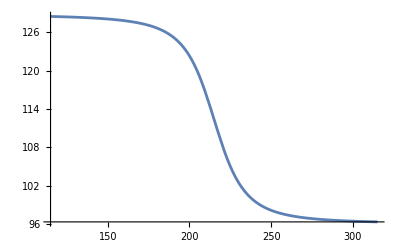

```mathematica
Plot[Ft[v,t0,d0,fs,c,tp],{tp,t0-100,t0+100}]
```

### add plotting details color convention is: red t0 (at ymid), blue tp0

```mathematica
ybot =Frecede[v,fs,c];
ytop=Fapproach[v,fs,c];
ymid=Fmean[v,fs,c];
```

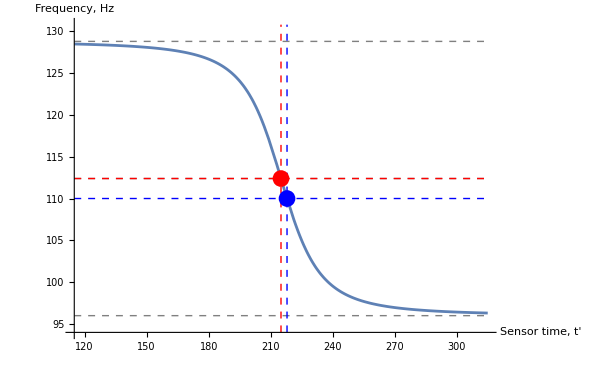

```mathematica
Plot[Ft[v,t0,d0,fs,c,tp],{tp,t0-100,t0+100},PlotRange->{All,{ybot-2,ytop+2}},AxesLabel->{"Sensor time, t'","Frequency, Hz"},ImageSize->600,Epilog->{{Dashed,Gray,Line[{{t0-100,#},{t0+100,#}}]&/@{ybot,ymid,ytop}},{Dashed,Red,Line[{{t0-100,Ft[v,t0,d0,fs,c,t0]},{t0+100,Ft[v,t0,d0,fs,c,t0]}}]},{Dashed,Blue,Line[{{t0-100,Ft[v,t0,d0,fs,c,tp0]},{t0+100,Ft[v,t0,d0,fs,c,tp0]}}]},{Dashed,Red,Line[{{t0,ybot-2},{t0,ytop+2}}]},{Dashed,Blue,Line[{{tp0,ybot-2},{tp0,ytop+2}}]},{Red,PointSize[0.02],Point[{t0,Ft[v,t0,d0,fs,c,t0]}]},{Blue,PointSize[0.02],Point[{tp0,Ft[v,t0,d0,fs,c,tp0]}]}}]
```

### values at tp = tp0 fs is less than Fmean by the factor Fratio

```mathematica
Fratio[v,c]
Fmean[v,fs,c]
fs
Fratio[v,c]Fmean[v,fs,c]
```

0.97875

112.388

110.

110.

### values at tp = tp0

```mathematica
Ft[v,t0,d0,fs,c,tp0]
FfactorA[v,t0,d0,c,tp0]
FfactorAt0[v,c]
Ffactor[v,t0,d0,c,tp0]
```

110.

6.61415×10^-18

0.0212496

1.

### values at tp = t0

```mathematica
Ft[v,t0,d0,fs,c,t0]
FfactorA[v,t0,d0,c,t0]
FfactorAt0[v,c]
Ffactor[v,t0,d0,c,t0]
```

112.388

0.0212496

0.0212496

0.97875

## Illustrate the ratios F(tp0) / F(t0) and dF/dtp(tp0) / dF/dtp(t0), for fixed d0.

### Technically we do not need to define this function, but it helps to emphasize the dependence on d0. The other parameters (v, t0, fs, c) are fixed.

```mathematica
Fvaryd0[d0_,tp_]:=Ft[v,t0,d0,fs,c,tp]
```

### Show how curves vary with changing d0:

```mathematica
Pcen={t0,Fvaryd0[99,t0]}
```

{215.,112.388}

```mathematica
Fvaryd0[99,t0]
Fvaryd0[d0,t0+d0/c]
fs
```

112.388

110.

110.

```mathematica
d0Vals=Range[500,4000,500];
thwid=40;
n=Length[d0Vals];
t0pVals=t0+d0Vals/c;
```

### Plots for F[ ]

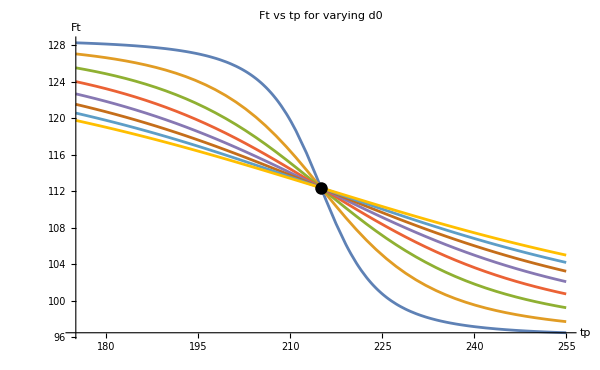

```mathematica
Plot[Evaluate@Table[Fvaryd0[d0,tp],{d0,d0Vals}],{tp,t0-thwid,t0+thwid},PlotRange->All,AxesLabel->{"tp","Ft"},PlotLabel->"Ft vs tp for varying d0",Epilog->{Black,PointSize[0.015],Point[Pcen]},ImageSize->600]
```

{{216.458,110.},{217.915,110.},{219.373,110.},{220.831,110.},{222.289,110.},{223.746,110.},{225.204,110.},{226.662,110.}}

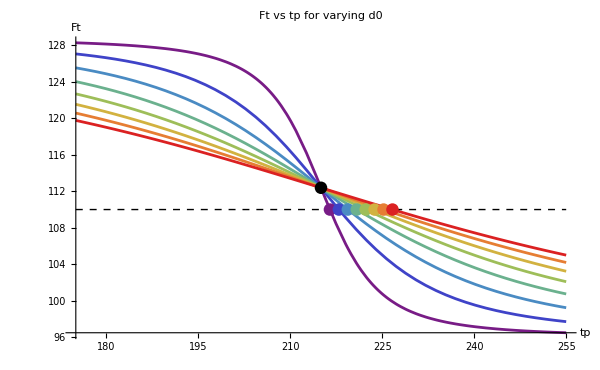

```mathematica
colors=Table[ColorData["Rainbow"][(i-1)/(n-1)],{i,n}];
tpAt=Table[t0+d0Vals[[i]]/c,{i,n}];
pts=Table[{tpAt[[i]],Fvaryd0[d0Vals[[i]],tpAt[[i]]]},{i,n}]
dots=Table[{colors[[i]],PointSize[0.015],Point[pts[[i]]]},{i,n}];
Plot[Evaluate@Table[Fvaryd0[d0,tp],{d0,d0Vals}],{tp,t0-thwid,t0+thwid},PlotRange->All,PlotStyle->colors,AxesLabel->{"tp","Ft"},PlotLabel->"Ft vs tp for varying d0",ImageSize->600,Epilog->Join[{{Black,Dashed,Thick,Line[{{t0-thwid,fs},{t0+thwid,fs}}]}},dots,{{Black,PointSize[0.015],Point[Pcen]}}]]
```

```mathematica
tblData=Table[{d0Vals[[i]],t0,t0pVals[[i]],Fvaryd0[d0Vals[[i]],t0],Fvaryd0[d0Vals[[i]],t0pVals[[i]]],Fvaryd0[d0Vals[[i]],t0pVals[[i]]]/Fvaryd0[d0Vals[[i]],t0]},{i,n}];
tbl=Grid[Prepend[Map[{NumberForm[#[[1]],{8,0}],NumberForm[#[[2]],{12,2}],NumberForm[#[[3]],{12,2}],NumberForm[#[[4]],{12,3}],NumberForm[#[[5]],{12,3}],NumberForm[#[[6]],{10,4}]}&,N@tblData],{"d0","t0","t0p = t0 + d0/c","F(t0)","F(t0p)","F(t0p)/F(t0)"}],Frame->All,Alignment->Center,Spacings->{2,1},Background->{{LightGray,None},None}]
```

d0 | t0 | t0p = t0 + d0/c | F(t0) | F(t0p) | F(t0p)/F(t0)
500. | 215.00 | 216.46 | 112.388 | 110.000 | 0.9788
1000. | 215.00 | 217.92 | 112.388 | 110.000 | 0.9788
1500. | 215.00 | 219.37 | 112.388 | 110.000 | 0.9788
2000. | 215.00 | 220.83 | 112.388 | 110.000 | 0.9788
2500. | 215.00 | 222.29 | 112.388 | 110.000 | 0.9788
3000. | 215.00 | 223.75 | 112.388 | 110.000 | 0.9788
3500. | 215.00 | 225.20 | 112.388 | 110.000 | 0.9788
4000. | 215.00 | 226.66 | 112.388 | 110.000 | 0.9788

### The value in the final column is this:

```mathematica
Fratio[v,c]
```

0.97875

### Plots for dF/dtp[ ]

```mathematica
DFvaryd0[d0_,tp_]:=D1F[v,t0,d0,fs,c,tp];
```

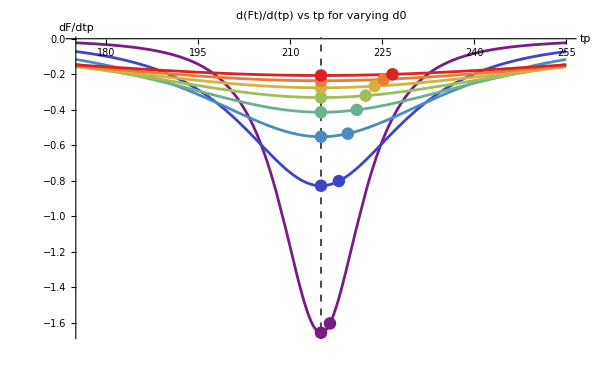

```mathematica
dpts1=Table[{t0pVals[[i]],DFvaryd0[d0Vals[[i]],t0pVals[[i]]]},{i,n}]; 
dpts2=Table[{t0,DFvaryd0[d0Vals[[i]],t0]},{i,n}]; 
ddots1=Table[{colors[[i]],PointSize[0.015],Point[dpts1[[i]]]},{i,n}];
ddots2=Table[{colors[[i]],PointSize[0.015],Point[dpts2[[i]]]},{i,n}];
plt=Plot[Evaluate@Table[DFvaryd0[d0,tp],{d0,d0Vals}],{tp,t0-thwid,t0+thwid},PlotRange->All,PlotStyle->colors,AxesLabel->{"tp","dF/dtp"},PlotLabel->"d(Ft)/d(tp) vs tp for varying d0",ImageSize->600,Epilog->Join[{{Black,Dashed,Thick,Line[{{t0,-10^9},{t0,10^9}}]}},ddots1,ddots2,{{Black,PointSize[0.015],Point[Pcen]}} ]]
```

```mathematica
tblData=Table[{d0Vals[[i]],t0,t0pVals[[i]],DFvaryd0[d0Vals[[i]],t0],DFvaryd0[d0Vals[[i]],t0pVals[[i]]],DFvaryd0[d0Vals[[i]],t0pVals[[i]]]/DFvaryd0[d0Vals[[i]],t0]},{i,n}];
tbl=Grid[Prepend[Map[{NumberForm[#[[1]],{8,0}],NumberForm[#[[2]],{12,2}],NumberForm[#[[3]],{12,2}],NumberForm[#[[4]],{12,3}],NumberForm[#[[5]],{12,3}],NumberForm[#[[6]],{10,4}]}&,N@tblData],{"d0","t0","t0p = t0 + d0/c","dF/dtp(t0)","dF/dtp(t0p)","dF(tp0)/dF(t0)"}],Frame->All,Alignment->Center,Spacings->{2,1},Background->{{LightGray,None},None}]
```

d0 | t0 | t0p = t0 + d0/c | dF/dtp(t0) | dF/dtp(t0p) | dF(tp0)/dF(t0)
500. | 215.00 | 216.46 | -1.656 | -1.603 | 0.9683
1000. | 215.00 | 217.92 | -0.828 | -0.802 | 0.9683
1500. | 215.00 | 219.37 | -0.552 | -0.534 | 0.9683
2000. | 215.00 | 220.83 | -0.414 | -0.401 | 0.9683
2500. | 215.00 | 222.29 | -0.331 | -0.321 | 0.9683
3000. | 215.00 | 223.75 | -0.276 | -0.267 | 0.9683
3500. | 215.00 | 225.20 | -0.237 | -0.229 | 0.9683
4000. | 215.00 | 226.66 | -0.207 | -0.200 | 0.9683

### This is the value in the final column. Since Fratio is < 1, D1Fratio < Fratio, meaning that the relative shift in the slopes is larger than the relative shift in the function evaluations.

```mathematica
Fratio[v,c]
(Fratio[v,c])^(3/2)
D1Fratio[v,c]
```

0.97875

0.968295

0.968295

## What about the function t[ ]?

```mathematica
thwid=40;
```

#### Let’s think about the angle gamma first. See SinGammat[] and SinGamma[] above. In terms of aircraft time t:

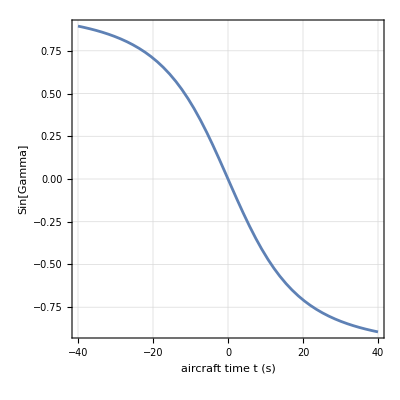

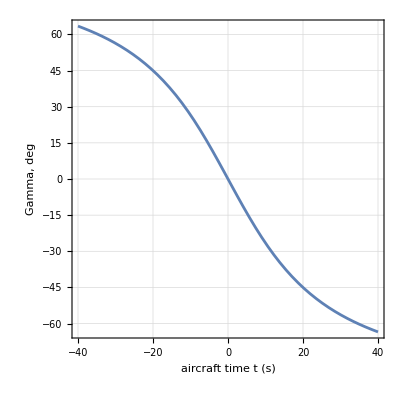

```mathematica
Plot[SinGammat[v,d0,t],{t,-thwid,thwid},Frame->True,Axes->False,AspectRatio->1,PlotRange->All,GridLines->Automatic,FrameLabel->{Style["aircraft time t (s)",16,Bold],Style["Sin[Gamma]",16,Bold]}]
Plot[ArcSin[SinGammat[v,d0,t]]180/Pi,{t,-thwid,thwid},Frame->True,Axes->False,AspectRatio->1,PlotRange->All,GridLines->Automatic,FrameLabel->{Style["aircraft time t (s)",16,Bold],Style["Gamma, deg",16,Bold]}]
```

```mathematica
Plot[SinGammat[v,d0,t],{t,-thwid,thwid},Frame->True,Axes->False,AspectRatio->1,PlotRange->All,GridLines->Automatic,FrameLabel->{Style["aircraft time t (s)",16,Bold],Style["Sin[Gamma]",16,Bold]}]
Plot[ArcSin[SinGammat[v,d0,t]]180/Pi,{t,-thwid,thwid},Frame->True,Axes->False,AspectRatio->1,PlotRange->All,GridLines->Automatic,FrameLabel->{Style["aircraft time t (s)",16,Bold],Style["Gamma, deg",16,Bold]}]
```

-Graphics-

-Graphics-

#### In terms of sensor time tp:

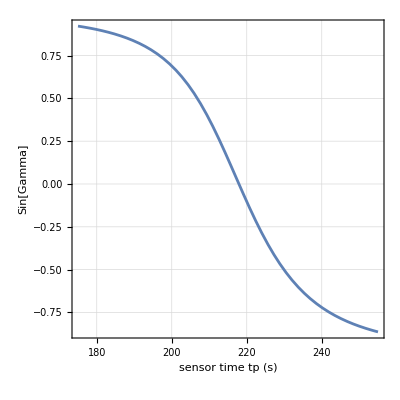

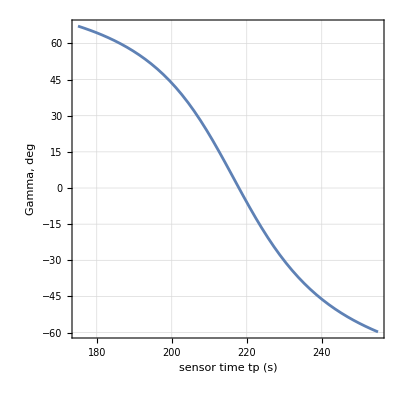

```mathematica
Plot[SinGamma[v,t0,d0,c,tp],{tp,t0-thwid,t0+thwid},Frame->True,Axes->False,AspectRatio->1,PlotRange->All,GridLines->Automatic,FrameLabel->{Style["sensor time tp (s)",16,Bold],Style["Sin[Gamma]",16,Bold]}]
Plot[ArcSin[SinGamma[v,t0,d0,c,tp]]180/Pi,{tp,t0-thwid,t0+thwid},Frame->True,Axes->False,AspectRatio->1,PlotRange->All,GridLines->Automatic,FrameLabel->{Style["sensor time tp (s)",16,Bold],Style["Gamma, deg",16,Bold]}]
```

#### Function t[ t’ ] For starters, we can see it is nonlinear:

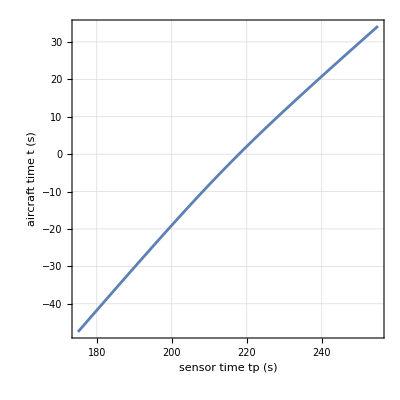

```mathematica
Plot[t[v,t0,d0,c,tp],{tp,t0-40,t0+40},Frame->True,Axes->False,AspectRatio->1,PlotRange->All,GridLines->Automatic,FrameLabel->{Style["sensor time tp (s)",16,Bold],Style["aircraft time t (s)",16,Bold]}]
```

#### Let’s start by finding the root of t[ t’ ], numerically and analytically. It differs from t0 by d0/c.

```mathematica
t0
tprootstart=t0;
troot=tp/. FindRoot[t[v,t0,d0,c,tp]==0,{tp,tprootstart}]
tp0
```

215.

217.915

217.915

```mathematica
t0-troot
-d0/c
```

-2.91545

-2.91545

#### It is clear that tp0 is not equal to -d0/c. Here’s a numerical check.

```mathematica
tp0
```

217.915

```mathematica
t0x=t[v,t0,d0,c,t0]
-d0/c
t0x/(-d0/c)
(1-v^2/c^2)^(-1/2)
```

-2.94693

-2.91545

1.0108

1.0108

#### Determine the asymptotes and their intersection

```mathematica
t0
v/c
tr[tp_]:=(tp-t0)/(1+v/c); 
tl[tp_]:=(tp-t0)/(1-v/c);
```

215.

0.145773

#### Plot

```mathematica
psz =0.03;
styles={Directive[Black,Thick],
Directive[Red,Dashed,Thick],
Directive[Blue,Dashed,Thick]};

legend=Placed[LineLegend[styles,{
"t(tp)",
"(tp - t0) / (1 + v/c)",
"(tp - t0) / (1 - v/c)"}],{0.3,0.85}];
```

```mathematica
ttprimePlotXY[tmin_,tmax_,ymin_,ymax_]:=Legended[Plot[t[v,t0,d0,c,tp],{tp,tmin,tmax},Frame->True,Axes->False,AspectRatio->1,PlotRange->{{tmin,tmax},{ymin,ymax}},PlotRangeClipping->True,GridLines->Automatic,FrameLabel->{Style["sensor  time  tp (s)",16,Bold],Style["aircraft  time  t (s)",16,Bold]},PlotStyle->styles[[1]],Epilog->{{styles[[2]],Line[{{tmin,tr[tmin]},{tmax,tr[tmax]}}]},{styles[[3]],Line[{{tmin,tl[tmin]},{tmax,tl[tmax]}}]},{Blue,PointSize[psz],Point[{troot,0}]},{Black,PointSize[psz],Point[{t0,0}]},{Red,PointSize[psz],Point[{t0,t0x}]} }],legend];
```

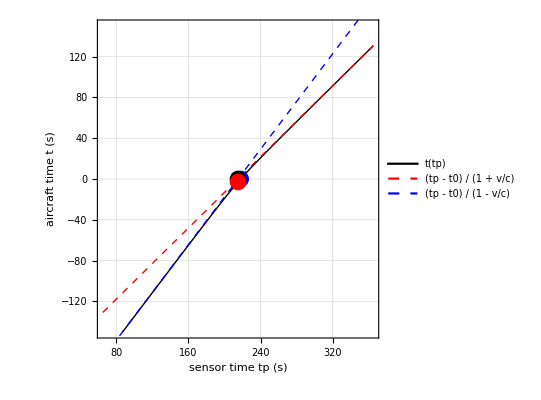

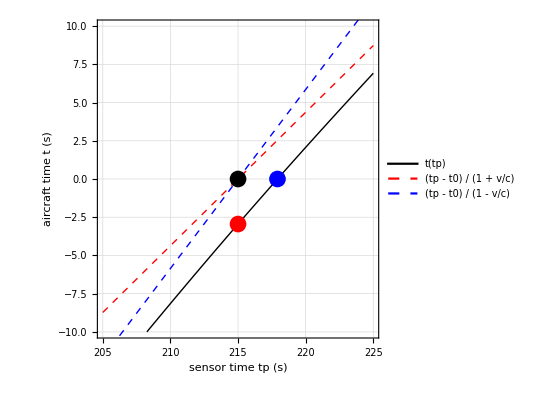

```mathematica
dtp = 150;ttprimePlotXY[t0-dtp,t0+dtp,-dtp,dtp]
dtp = 10;ttprimePlotXY[t0-dtp,t0+dtp,-dtp,dtp]
```

#### What about the inverse of this plot? This is the function tp[ t ], which is sensor time.

```mathematica
tpfun[t_]:=t+t0+√(d0^2+(v t)^2)/c;
```

```mathematica
legend2=Placed[LineLegend[styles,{
"tp(t)",
"t0 + (1 + v/c) t",
"t0 + (1 − v/c) t"}],{0.25,0.85}];
```

```mathematica
tpfunPlotXY[tmin_,tmax_,ymin_,ymax_]:=Legended[Plot[tpfun[t],{t,tmin,tmax},Frame->True,Axes->False,AspectRatio->1,PlotRange->{{tmin,tmax},{ymin,ymax}},GridLines->Automatic,FrameLabel->{Style["aircraft  time  t (s)",16,Bold],Style["sensor  time  tp (s)",16,Bold]},PlotStyle->styles[[1]],Epilog->{{styles[[2]],Line[{{tmin,t0+(1+v/c) tmin},{tmax,t0+(1+v/c) tmax}}]},{styles[[3]],Line[{{tmin,t0+(1-v/c) tmin},{tmax,t0+(1-v/c) tmax}}]},{Blue,PointSize[psz],Point[{0,troot}]},{Black,PointSize[psz],Point[{0,t0}]},{Red,PointSize[psz],Point[{t0x,t0}]} }],legend2];
```

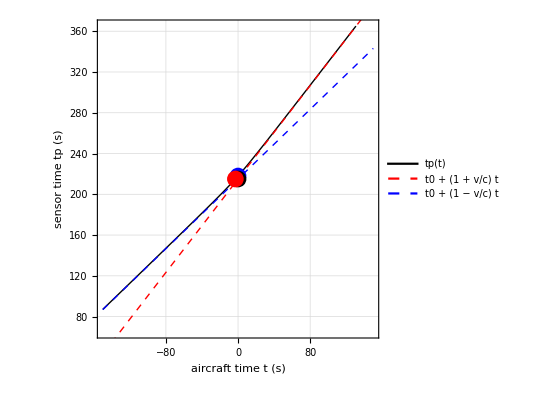

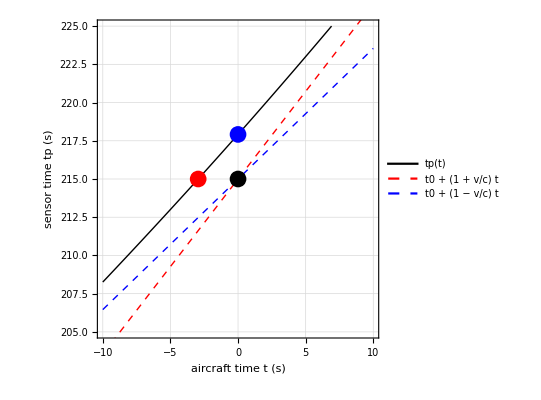

```mathematica
dtp=150;tpfunPlotXY[-dtp,dtp,t0-dtp,t0+dtp]
dtp=10;tpfunPlotXY[-dtp,dtp,t0-dtp,t0+dtp]
```

## Miscellaneous

### example values

```mathematica
Fapproach[v,fs,c]
Frecede[v,fs,c]
Fmean[v,fs,c]
fs
fs/Fmean[v,fs,c]
1-(v/c)^2
1-((c/2)/c)^2
```

128.771

96.0051

112.388

110.

0.97875

0.97875

0.75

### approximations for the Fapproach and Frecede frequencies

```mathematica
Frange[v,fs,c]
Frangeapprox4[v,fs,c]
Frangeapprox2[v,fs,c]
```

32.7662

32.7514

32.07

## estimating detection distance

### The calculations assume a straight flight path and a constant speed v. From the paper: “For example, the seismic signal of the Cessna in Figure 2 flying at 69 m/s emerges from background noise levels at ∼93 s prior to the closest approach of the aircraft (t0). Inserting t’ = t0 − 93 s into equation (2) gives a detection distance of 7.6 km.” Note that the value of 7.6 is based on ESTIMATED values of c, d0, and v.

```mathematica
t0=116.18      (* estimated: listed on Figure 2  *)
txp=23.92;     (* measurement from spectrogram *)
dt=t0-txp     (* matches the ~93 s value in the paper *)
```

116.18

92.26

```mathematica
c =313.11;d0=1142.38;v=64.27;      (* estimated: values from the header of FIgure 2b *)
t0p=t0+d0/c     (* matches the 119.83 value in the legend of Figure 2b *)
t[v,t0,d0,c,t0p]
texact=t[v,t0,d0,c,txp]
dpath=texact v      (* distance along path from detecton to closest approach *)
ddetect=√(d0^2+dpath^2)     (* matches the 7.6 km value in the paper *)
```

119.828

6.0271×10^-15

-116.437

-7483.42

7570.11

### use an approximation for t[ ] (see tr[ ] and tl[ ] above)

```mathematica
tapprox=(txp-t0)/(1-v/c)
dpath=tapprox v
ddetect=√(d0^2+dpath^2)
```

-116.089

-7461.03

7547.97

### time values note: the difference of 1.4 s is close to the median difference shown in Figure S5, panel 3

```mathematica
Trefp=1550781214.001998;      (* Figure 2a title: 2019-02-21 20:33:34.001998 *)
T0=1550781331.5739982;          (* 2019-02-21 20:35:31.574 *)
t0gt=T0-Trefp          (* ground-truth: from flight path database *)
t0
t0-t0gt
```

117.572

116.18

-1.392

### calculations based on ground truth values

```mathematica
c =328.01;d0=952.18;v=69.45;      (* ground truth *)
t0p=t0gt+d0/c
texact=t[v,t0gt,d0,c,txp]
dpath=texact v 
ddetect=√(d0^2+dpath^2)
```

120.475

-119.019

-8265.84

8320.51